Define equation 7.35 in my master thesis. Plot the results. This is used in Figure 7.3 (plotted in Python for consistent style).

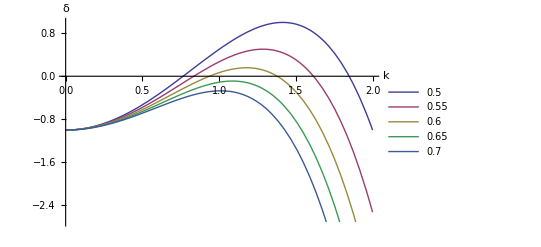

```mathematica
ClearAll["Global`*"]
σ[k_,δ_]:= -δ k^4+k^2/δ-1
Plot[Evaluate@Table[σ[k,δ],{δ,0.5,0.7,0.05}],{k,0,2.0},PlotLegends->Range[0.5,0.7,0.05],AxesLabel->{"k","δ"}]
```

Solve equation 7.35 == 0 for k using a range of δ values. Then calculate the corresponding L values. The L values are in tuples of (L_low, L_high), both corresponding to the same δ value. The Riffle function makes the δ array correspond to the L array, and the Partition function puts them together correctly. The result is plotted.

The 2-periodic theoretical DFT curve is just 2 times the Pts array.
To export the Pts1.csv and Pts2.csv used in the Python code, comment out the Export function.

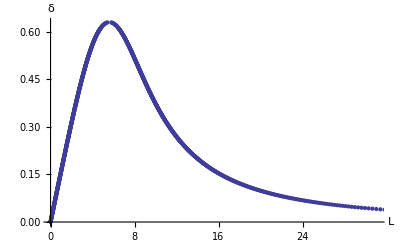

```mathematica
ks = k/.Evaluate@Table[Solve[σ[k,δ]==0&&k≥0],{δ,0.001,(1/4)^(1/3)-0.00000000001,0.001}];
L = Flatten[(2π)/ks];
deltas = Range[0.001,(1/4)^(1/3)-0.00000000001,0.001];
deltas = Riffle[deltas,deltas];
Pts = Partition[Riffle[L,deltas],2];
(*Export["Pts.csv",Pts]*)
L1 =ListPlot[Pts,AxesLabel->{"L","δ"}]
```

Here is a k_crit solver.

```mathematica
δ = (1/4)^(1/3);
kcrit=k/. Solve[-δ k^4+k^2/δ-1==0&&k≥0,k];
N[kcrit]
```

{1.12246,1.12246}

And here is an L_crit solver.

```mathematica
Lcrit = (2π)/kcrit;
N[Lcrit]
```

{5.59768,5.59768}